```mathematica
(* L1-norm calculation for MEMS-state under correlated-depolarizing channel with memory: *)
```

```mathematica
(* Defining uncorrelated-depolarizing channel Kraus Operators for single qubit: *)
ClearAll[g,γ, μ,  p];
$Assumptions=p ≥  0 && √(1-p)≥ 0 && Element[√(1-p),Reals];
E0=√(1-p) PauliMatrix[0];
E1=√(p/3) PauliMatrix[1];
E2=√(p/3) PauliMatrix[2];
E3=√(p/3) PauliMatrix[3];
Es={{E0,E1,E2,E3}};

(* Checking the completenes condition:*)
 FullSimplify[Sum[ConjugateTranspose[Es[[1,i]]]. Es[[1,i]],{i,1,4}]]//MatrixForm ;

(* Uncorrelated-Depolarizing channel Kraus operators for two-qubits:  *)
 eu=Table[KroneckerProduct[Es[[1,i]],Es[[1,j]]],{i,1,4},{j,1,4}] ;

(* Correlated-depolarizing channel Kraus operators for two qubits: *)
ec0 =√(1-p) KroneckerProduct[PauliMatrix[0],PauliMatrix[0]] ;
ec1 =√(p/3)  KroneckerProduct[PauliMatrix[1],PauliMatrix[1]] ;
ec2 =√(p/3) KroneckerProduct[PauliMatrix[2],PauliMatrix[2]] ;
ec3 =√(p/3) KroneckerProduct[PauliMatrix[3],PauliMatrix[3]] ;
ec={{ec0, ec1, ec2, ec3}};

(* Checking the completeness of the Kraus operators: *)
FullSimplify[Sum[ConjugateTranspose[eu[[i,j]]].eu[[i,j]],{i,1,4},{j,1,4}]]//MatrixForm;
FullSimplify[Sum[ConjugateTranspose[ec[[1,i]]].ec[[1,i]],{i,1,4}]]//MatrixForm;
```

```mathematica
(* MEMS-state density Matrix *)
ClearAll[g,γ,p,μ];
 ρ={{g,0,0,γ/2},{0,1-2g,0,0},{0,0,0,0},{γ/2,0,0,g}};
ρ//MatrixForm;
Tr[ρ];

(* Density Matrix after evolution in ADC: *)
ρ2=(1-μ)*Sum[eu[[i,j]].ρ.ConjugateTranspose[eu[[i,j]]],{i,1,4},{j,1,4}]+μ*Sum[ec[[1,i]].ρ.ConjugateTranspose[ec[[1,i]]],{i,1,4}]; 

Simplify[Tr[ρ2]]
FullSimplify[ρ2]//MatrixForm
```

1

(-1/9 (g (3-4 p)^2+2 (3-2 p) p) (-1+μ)+g μ | 0 | 0 | 1/18 γ (9-8 p (-3+2 p) (-1+μ))
0 | 1/9 (-3+2 p) (-3+g (6+8 p (-1+μ))-2 p (-1+μ)) | 0 | 0
0 | 0 | 2/9 p (-2 (g (3-4 p)+p) (-1+μ)+(3-6 g) μ) | 0
1/18 γ (9-8 p (-3+2 p) (-1+μ)) | 0 | 0 | -1/9 (g (3-4 p)^2+2 (3-2 p) p) (-1+μ)+g μ)

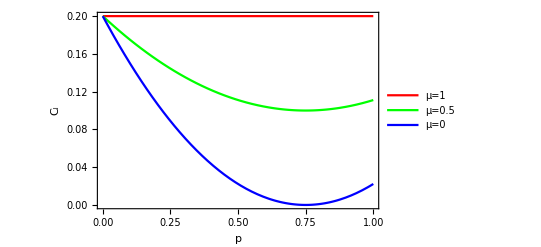

```mathematica
(*L1-norm of coherence for MEMS state: γ < 2/3 *)
ClearAll[g,γ, μ,  p];
γ=0.2;
g=1/3;
L1=Sum[If[i!=j,Abs[ρ2[[i,j]]],0],{i,1,4},{j,1,4}];
Plot[Evaluate@Table[L1,{μ,{1,0.5,0}}],{p,0,1},FrameLabel->{"p","C_l"},PlotLegends->{"μ=1", "μ=0.5","μ=0"},PlotStyle->{Red, Green, Blue},Frame-> True, FrameStyle->Directive[Black,12]]
```

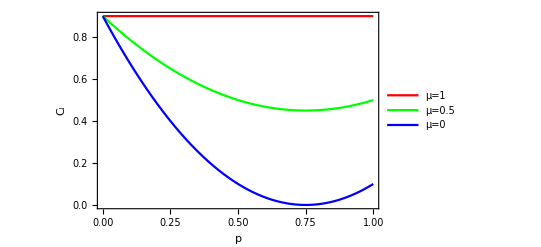

```mathematica
(*L1-norm of coherence for MEMS state: γ>2/3 *)
ClearAll[g,γ, μ,  p];
γ=0.9;
g=γ/2;
L1=Sum[If[i!=j,Abs[ρ2[[i,j]]],0],{i,1,4},{j,1,4}];
Plot[Evaluate@Table[L1,{μ,{1,0.5,0}}],{p,0,1},FrameLabel->{"p","C_l"},PlotLegends->{"μ=1", "μ=0.5","μ=0"},PlotStyle->{Red, Green, Blue},Frame-> True, FrameStyle->Directive[Black,12]]
```

```mathematica
rhotilde[state_]:=(KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]).(Conjugate[state].(KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]));
  rhocon[state_]:=state.rhotilde[state];
eigensqrt[state_]:=Re[Sqrt[Eigenvalues[rhocon[state]]]];
order[state_]:=Sort[eigensqrt[state],Greater];
concurr[state_]:=Max[0,order[state][[1]]-order[state][[2]]-order[state][[3]]-order[state][[4]]];
```

```mathematica
γ=0.5;
g=1/3;
μ=0;
```

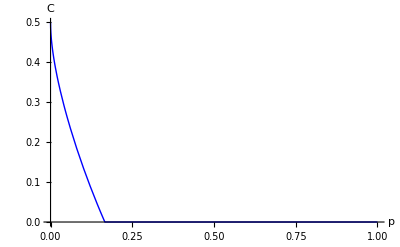

0

```mathematica
p1=Plot[N[concurr[ρ2]],{p,0,1},AxesLabel->{"p","C"},PlotRange->All,LabelStyle->{FontSize->22, Black,Bold},PlotRange->{0,0.8}, PlotStyle->Blue]
```

```mathematica
γ=0.5;
g=1/3;
μ=0.5;
```

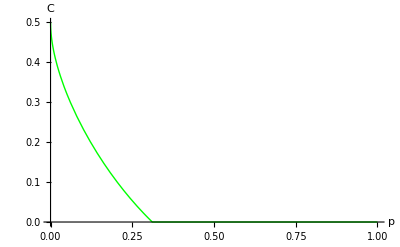

```mathematica
p2=Plot[N[concurr[ρ2]],{p,0,1},AxesLabel->{"p","C"},PlotRange->All,LabelStyle->{FontSize->22, Black,Bold},PlotRange->{0,0.8}, PlotStyle->Green]
```

```mathematica
γ=.5;
g=1/3;
μ=1;
```

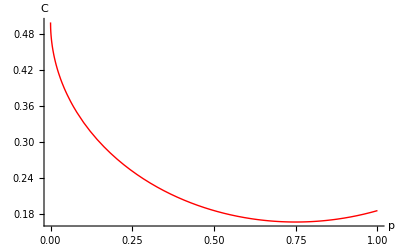

```mathematica
p3=Plot[N[concurr[ρ2]],{p,0,1},AxesLabel->{"p","C"},PlotRange->All,LabelStyle->{FontSize->22, Black,Bold},PlotRange->{0,0.8}, PlotStyle->Red]
```

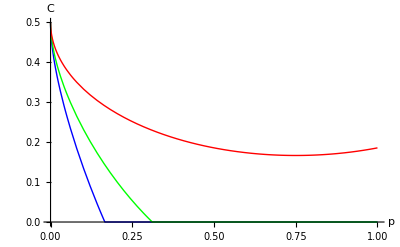

```mathematica
p4=Show[p1,p2,p3,PlotRange->All,FrameLabel->{"p","Concurrence"}, FrameStyle->Directive[Black,12]]
```